```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/expVal_Rho2.nb"];
NotebookEvaluate["modules/find_minimum.nb"];
On[Assert]
```

```mathematica
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero]
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
{t1time,t1}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time]
{t2time,t2}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time]

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

Time taken to compute t1: 7.04044

Time taken to compute t2: 6.58577

ΔE smaller than 1x10^-6, breaking search after 21 steps. ΔE: 7.70367×10^-7

{ω_min, E_min}: {0.599673,2.46536}

Plot of gradient descent.

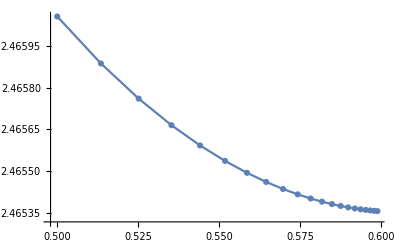

Time taken to find minimum: 74.2s

{ω_min,E_min}: {0.599673,2.46536}

Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): {0.728541,0.611674,0.701826}

Expectation Values as ratios: {1.,0.704908,0.928007}

Expectation Values of <λ_i^2> {λ_3, λ_1, λ_2} in (fm^2): {0.294717,0.433624,0.335513}

Expectation Values as ratios: {1.,1.47132,1.13843}

```mathematica
(* Find minimum *)
learningRate=1;
nSteps=30;
{minTime,min}=Timing[findMinimum[learningRate,nSteps]];
wMin=min[[1]];
data=min[[3]];

Print["Plot of gradient descent."]
ListPlot[data,Joined->True,PlotMarkers->Automatic]

Print["Time taken to find minimum: ",DecimalForm[minTime,3],"s"]
Print["{ω_min,E_min}: ",{min[[1]],min[[2]]}]

expValsRho=expValRho[J,P,Isospin,Λ,γMax,wMin,m1,m2,m3,project,2];
Print["Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): ",√expValsRho/5.068]
Print["Expectation Values as ratios: ",expValsRho/expValsRho[[1]]]
expValsLam=expValLam[J,P,Isospin,Λ,γMax,wMin,m1,m2,m3,project,2];
Print["Expectation Values of <λ_i^2> {λ_3, λ_1, λ_2} in (fm^2): ",expValsLam/5.068^2]
Print["Expectation Values as ratios: ",expValsLam/expValsLam[[1]]]
```

```mathematica
(* Calculating mean mass-square radiu using approximate method *)
expVals=√expValsRho/5.068;
a=expVals[[1]];
b=expVals[[2]];
c=expVals[[3]];
triangle=SSSTriangle[b,a,c];
pos1=triangle[[1,1]];
pos3=triangle[[1,2]];
pos2=triangle[[1,3]];
xcom=(m2*pos2[[1]]+m3*pos3[[1]])/(m1+m2+m3);
ycom=(m2*pos2[[2]])/(m1+m2+m3);
com={xcom,ycom};
dr1=Norm[(pos1-com)^2];
dr2=Norm[(pos2-com)^2];
dr3=Norm[(pos3-com)^2];
dist=(m1*dr1)/(m1+m2+m3)+(m2*dr2)/(m1+m2+m3)+(m3*dr3)/(m1+m2+m3)
```

0.094384

```mathematica
(* Mean mass-square radius using exact method *)
expVals=expValsLam/5.068^2;
λ3Squared=expVals[[1]];
λ1Squared=expVals[[2]];
λ2Squared=expVals[[3]];
M=m1+m2+m3;
term1=(m1(m2+m3)^2)/M^3 λ1Squared;
term2=(m2(m1+m3)^2)/M^3 λ2Squared;
term3=(m3(m1+m2)^2)/M^3 λ3Squared;
RmSquared=term1+term2+term3
```

0.104501